# Extending SML Package - Hierarchical Solver for the Stationary Distribution on the boundaries of a Markov One-step Process

## Method

## Functions

### Function discription

This function calculates zeros of a list.....
La la

```mathematica
DiscreteZero[vecXY_List]:=With[{initSize=5},
Module[{Z=Length[vecXY]-1,xtemp=0.,dxtemp=0.,vsize=initSize,nzeros=0,Output},


Output=Rest[Reap[
Do[
If[vecXY[[i,2]]>= 0&&vecXY[[i+1,2]]< 0,

If[vecXY[[i,2]]== 0&&i>1,
Sow[(vecXY[[i+1,2]]-If[i>1,vecXY[[i-1,2]],vecXY[[i,2]]])/(vecXY[[i+1,1]]-If[i>1,vecXY[[i-1,1]],vecXY[[i,1]]]),dx];
Sow[vecXY[[i,1]],x]; 

Sow[i,index];
,
dxtemp=(vecXY[[i+1,2]]-vecXY[[i,2]])/(vecXY[[i+1,1]]-vecXY[[i,1]]);
xtemp=vecXY[[i,1]]-vecXY[[i,2]]/((vecXY[[i+1,2]]-vecXY[[i,2]])/(vecXY[[i+1,1]]-vecXY[[i,1]])); 

If[Abs[xtemp-vecXY[[i,1]]]<Abs[xtemp-vecXY[[i+1,1]]]&&i>1,

Sow[dxtemp,dx];
Sow[xtemp,x];
Sow[i,index];
,
If[i>1&&i<Z,
Sow[dxtemp,dx];
Sow[xtemp,x];
Sow[i+1,index];
];
];];];
,{i,1,Z}];
]][[1]];
If[Length@Output>0,
Transpose[Output],
{}
]
]
];
```

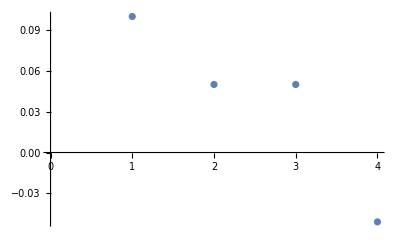

```mathematica
ListPlot[{0.2,0.55,0.4,0.000}-{0.1,0.5,0.35,0.051}]
```

```mathematica
DiscreteZero2[Transpose[{Range[0,1,1/3],{0.2,0.55,0.4,0.000}-{0.1,0.5,0.35,0.051}}]]
```

{{-0.303,0.831683,3}}

### Function discription

This function calculates zeros of a list.....
La la

```mathematica
TransitionsPairs::difdimensions="The lenght of the first list, `1`, is equal to that of the second, `2`.";
TransitionsPairs[Tp_List,Tm_List]:=If[Length[Tp]==Length[Tm],With[{Z=Length[Tp]-1},
Module[{zeros=DiscreteZero[Transpose@{Range[0,Z]/Z,Tp-Tm}], CoIindex={1,Z+1},Pp=1.,Pm=1.},

If[Length[zeros]>0,
CoIindex=Flatten@Insert[CoIindex,zeros[[All,-1]],2] ;


{Transpose@{
CoIindex, (* Point index, from 1 to Z+1 *)
Flatten[{0.,zeros[[All,2]],1.}],(*Point position from 0 to 1*)
Flatten[{1.,zeros[[All,1]],1.}],(*Drift derivative*)
Flatten[{1.,Table[(Tm[[CoIindex[[i]]]]+Tp[[CoIindex[[i]]]])/(2Z),{i,2,Length[CoIindex]-1}],1.}](*Diffusion*)
},
SparseArray[Flatten[Table[

(*Pp=1+∑_(j=CoI[[i]]+1)^(CoI[[i+1]]-1) ∏_(k=CoI[[i]]+1)^j Tm[[k]]/Tp[[k]];*)
Pp=1.;Do[Pp=1.+Pp Tm[[k]]/Tp[[k]];,{k,CoIindex[[i]]+1,CoIindex[[i+1]]-1}];
(*Pm=1+∑_(j=CoI[[i]]+1)^(CoI[[i+1]]-1) ∏_(k=CoI[[i]]+1)^j Tp[[k]]/Tm[[k]]*)
Pm=1.;Do[Pm=1.+Pm Tp[[k]]/Tm[[k]];,{k,CoIindex[[i+1]]-1,CoIindex[[i]]+1,-1}];
(*CoI[[i]] to CoI[[i+1]]  and   CoI[[i+1]] to CoI[[i]]*)

{{i,i+1}-> Tp[[CoIindex[[i]]]]/Pp,{i+1,i}->Tm[[CoIindex[[i+1]]]]/Pm}
,{i,1,Length[CoIindex]-1}]],{Length[CoIindex],Length[CoIindex]}]
},


{Transpose@{
CoIindex, (* Point index, from 1 to Z+1 *)
{0.,1.},(*Point position from 0 to 1*)
{1.,1.},(*Drift derivative*)
{1.,1.}(*Diffusion*)
},
SparseArray[

(*Pp=1+∑_(j=CoI[[i]]+1)^(CoI[[i+1]]-1) ∏_(k=CoI[[i]]+1)^j Tm[[k]]/Tp[[k]];*)
Pp=1.;Do[Pp=1.+Pp Tm[[k]]/Tp[[k]];,{k,2,Z}];
(*Pm=1+∑_(j=CoI[[i]]+1)^(CoI[[i+1]]-1) ∏_(k=CoI[[i]]+1)^j Tp[[k]]/Tm[[k]]*)
Pm=1.;Do[Pm=1.+Pm Tp[[k]]/Tm[[k]];,{k,Z,2,-1}];
(*CoI[[i]] to CoI[[i+1]]  and   CoI[[i+1]] to CoI[[i]]*)

{{1,2}-> Tp[[1]]/Pp,{2,1}->Tm[[Z+1]]/Pm}
,{Length[CoIindex],Length[CoIindex]}]
}


]

]]
,Message[TransitionsPairs::difdimensions,Dimensions[Tp],Dimensions[Tm]]];
```

```mathematica
TransitionsPairs[{0.2,0.55,0.4,0.1},{0.1,0.5,0.35,0.05}]
```

{{{1,0.,1.,1.},{4,1.,1.,1.}},SparseArray[<2>, {2, 2}]}

### Function discription

This function calculates zeros of a list.....
La la

```mathematica
StatDESML[s_,T_,Z_,par_List]:=
Module[{CoIFull={{0}},innerCoI={{0.}},ρTemp={{0}},ρ={{0}},pairId=0,zeros={{0.,0.,0}},TMat, vec={0.},speed={0.},temp
,innerCoIcount=0,
CoI=Table[{SparseArray[{i->Z},{s}],1.,1.},{i,1,s}]
},


temp=PrintTemporary["Computing CoI and Transitions"];
Monitor[

{innerCoI,ρ}=Rest[Reap[

Do[pairId++;

{zeros,ρTemp}=TransitionsPairs[Table[T[s2,s1,Z-i,Z,par],{i,0,Z}],Table[T[s1,s2,i,Z,par],{i,0,Z}]];

If[Length[zeros]>2,
Sow[Table[{
SparseArray[{s1->(zeros[[i,1]]-1),s2->(Z-(zeros[[i,1]]-1))},{s}],zeros[[i,3]],zeros[[i,4]]}
,{i,2,Length[zeros]-1}],CoIinfo];
,
Sow[{},CoIinfo];
];

Do[

Sow[{Which[array[[1,1]]==1,s2,array[[1,1]]==Length[ρTemp],s1,True,s+innerCoIcount+array[[1,1]]-1],Which[array[[1,2]]==1,s2,array[[1,2]]==Length[ρTemp],s1,True,s+innerCoIcount+array[[1,2]]-1]}->array[[2]],traMat];

,{array,ArrayRules[ρTemp][[1;;-2]]}];

innerCoIcount+=Length[zeros]-2;

,{s1,1,s-1},{s2,s1+1,s}];
]][[1]];

,ProgressIndicator[pairId/Binomial[s,2.]]];
NotebookDelete[temp];

innerCoI=Flatten[innerCoI,1];

temp=PrintTemporary["Flatten do CoI"];
CoI=Flatten[{CoI,innerCoI},1];
NotebookDelete[temp];

temp=PrintTemporary["Construcao da matriz"];
TMat=SparseArray[ρ,{1,1}(s+innerCoIcount)];
NotebookDelete[temp];

temp=PrintTemporary["Speed up matrix"];
(*Speed up matrix*)
speed=Total[Transpose@TMat];
TMat/=Max[speed];
speed/=Max[speed]; 
NotebookDelete[temp];

temp=PrintTemporary["Diagonal matrix"];
Monitor[
Do[
TMat[[i,i]]=1-speed[[i]];
,{i,1,Length@TMat}];,ProgressIndicator[i/Length@TMat]];
NotebookDelete[temp];

temp=PrintTemporary["Stat Dist"];
(*vec=NullSpace[Transpose@TMat];*)
vec=Eigenvectors[Transpose@TMat,1,Method->{"Arnoldi","Shift"->1.00000000001}];
NotebookDelete[temp];

temp=PrintTemporary["Renormalization"];
Which[
Length[vec]==0,
Print["Could not compute Stationary Distribution."];
vec=ConstantArray[0,Length@CoI];
,
Length[vec]>1,
Print["Stationary Distribution was computed but might contain errors."];
vec=vec[[-1]];
,
True,
vec=vec[[1]];

Do[
If[CoI[[i,2]]<0,vec[[i]]*=Z √(2π CoI[[i,3]]/(-CoI[[i,2]]))];
,{i,s+1,Length@vec}];
NotebookDelete[temp];

Print["Normalization"];
vec=vec/Total[vec];

];


{CoI[[All,1]],vec}
];
```

## Using the function

lalala game theory

```mathematica
Δf[i_,Z_,is_,β_]:=β(i-is)/Z;
Tp[i_,Z_,is_,β_,μ_]:=(Z-i)/Z(i/(Z-1)1/(1+ⅇ^(-Δf[i,Z,is,β]))(1-μ)+μ);
Tm[i_,Z_,is_,β_,μ_]:=i/Z((Z-i)/(Z-1)1/(1+ⅇ^Δf[i,Z,is,β])(1-μ)+μ);
T12[i_,Z_,is_,β_,μ_]:=i/Z((Z-i)/(Z-1)1/(1+ⅇ^Δf[i,Z,is,β])(1-μ)+μ);
T21[i_,Z_,is_,β_,μ_]:=i/Z((Z-i)/(Z-1)1/(1+ⅇ^(-Δf[Z-i,Z,is,β]))(1-μ)+μ);
T[fs_,ts_,k_,Z_,par_List]:=Module[{β=par[[1]],μ=par[[2]],is=par[[3]]},
If[fs==1&&ts==2,
T12[k,Z,is,β,μ],
If[fs==2&&ts==1,
T21[k,Z,is,β,μ],
If[fs==1&&ts==3,
T12[k,Z,is,β,μ],
If[fs==3&&ts==1,
T21[k,Z,is,β,μ],
If[fs==2&&ts==3,
T12[k,Z,is,β,μ],
If[fs==3&&ts==2,
T21[k,Z,is,β,μ],
"error"
]]]]]]];
```

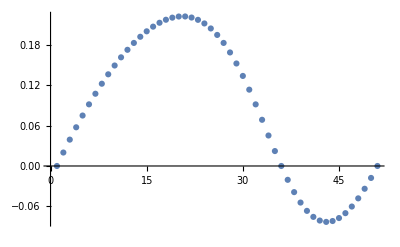

```mathematica
With[{Z=50,β=-10.,is=35,μ=1.2589254117941661*^-8},
ListPlot[Table[T[2,1,Z-i,Z,{β,μ,is}],{i,0,Z}]-Table[T[1,2,i,Z,{β,μ,is}],{i,0,Z}]]
]
```

```mathematica
With[{Z=50,β=-10.,is=35},
Print[StatDESML2[3,T,Z,{β,1.2589254117941661*^-8,is}]//Normal];
]
```

Flatten do CoI

Construcao da matriz

Speed up matrix

Diagonal matrix

Stat Dist

Renormalization

Normalization

Done

{{{50,0,0},{0,50,0},{0,0,50},{35,15,0},{35,0,15},{0,35,15}},{0.000584679,2.13383×10^-17,0.,0.499708,0.499708,-3.92298×10^-17}}

```mathematica
plotA=With[{Z=50,β=-10.,is=35},
Print[StatDESML2[2,T,Z,{β,1,is}]//Normal];
Monitor[data=Table[
Flatten@{μ,Plus@@Times@@StatDESML2[2,T,Z,{β,μ,is}]}
,{μ,10.^FindDivisions[Log10[{10^-13,10^0}],150]}];
,μ];
ListLogLinearPlot[
data[[All,{1,#}]]&/@Range[2,2], Joined->True
,PlotRange->{0,Z}]
]
```

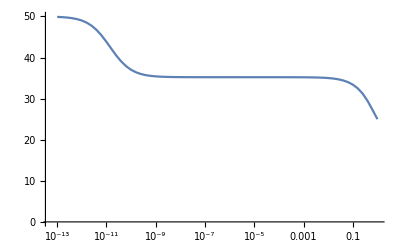

```mathematica
plotB=With[{Z=50,β=-10.,is=35},
Module[{Mat,vec},

Monitor[

data=Table[

Mat=SparseArray[{{i_,j_}/;j==i+1:>Tp[i-1,Z,is,β,μ],{i_,j_}/;j==i-1:>Tm[i-1,Z,is,β,μ],{i_,j_}/;j==i:>1-If[i<Z+1,Tp[i-1,Z,is,β,μ],0]-If[i>1,Tm[i-1,Z,is,β,μ],0]},{Z+1,Z+1}];
vec=Eigenvectors[Transpose[Mat],1,Method->{"Arnoldi", "Shift"->1.0000000001}][[1]];
vec=vec/Total[vec];
Flatten@{μ,(Plus@@Times@@{vec,Range[0,Z]})}
,{μ,10.^FindDivisions[Log10[{10^-13,10^-0}],100]}];
,μ];
ListLogLinearPlot[
data[[All,{1,#}]]&/@Range[2,2], Joined->True
,PlotRange->{0,Z}]




]
]
```

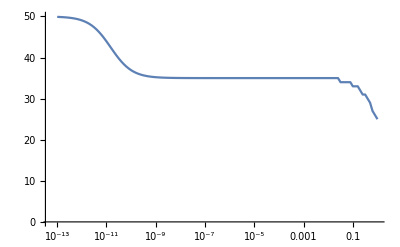
```mathematica
Show[{-Graphics-,-Graphics-}]
```